```mathematica
Experiment of college physics 2
Lihong Ao
2019271014
SZU,physics
```

```mathematica
金属电子逸出功
```

```mathematica
f(E)=1/(1+ⅇ^((E-Subscript[E, F])/kT))
```

```mathematica
Subscript[E, 0]=Subscript[E, b]-Subscript[E, f]=e U
```

```mathematica
I=A S T^2 ⅇ^((-e U)/(k t))
```

```mathematica
lg I/T^2=lg(A S)-5040U 1/T
```

```mathematica
Subscript[E, a]=Subscript[U, a]/(Subscript[r, 1] ln Subscript[r, 2]/Subscript[r, 1])
lg Subscript[I, a]=lg I+(0.439 √Subscript[U, a])/(2.3T √(Subscript[r, 1] ln Subscript[r, 2]/Subscript[r, 1]))
```

```mathematica
Ia={{4,4,4,4,4,4,4,5,5},{17,17,18,18,18,19,19,19,20},{59,60,61,62,63,65,66,67,70},{179,183,187,190,193,197,200,203,209},{490,501,512,521,530,538,547,555,566}};
T={1800,1880,1960,2040,2120};
```

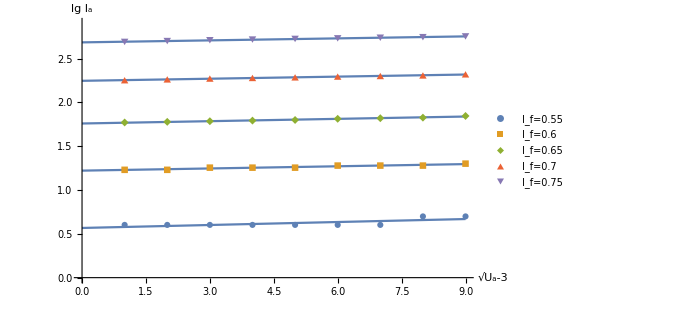

```mathematica
Clear[Subscript]
tab1=Table[Minimize[Sum[((Subscript[a, i] u+Subscript[b, i]-Log[10,Ia[[i]]])[[u]])^2,{u,1,Length@Ia[[i]]}],{Subscript[a, i],Subscript[b, i]}],{i,1,Length@Ia}];
Table[Subscript[a, i]=Subscript[a, i]/.(tab1[[i]][[2]]),{i,1,Length@Ia}];
Table[Subscript[b, i]=Subscript[b, i]/.(tab1[[i]][[2]])//Simplify,{i,1,Length@Ia}];
Show[Plot[Table[Subscript[a, i] u+Subscript[b, i],{i,1,Length@Ia}],{u,0,9},AxesLabel->{"√U_a-3","lg I_a"},ImageSize->500,PlotRange->{0,2.9}],ListPlot[Log[10,Ia],PlotMarkers->Automatic,PlotLegends->{"I_f=0.55","I_f=0.6","I_f=0.65","I_f=0.7","I_f=0.75"},ImageSize->500]]
```

```mathematica
lgI=Table[Subscript[b, i],{i,1,5}]-6//N
Log[10,10^lgI/T^2]-6//N
1/T//N
```

{-5.43294,-4.77881,-4.24084,-3.7538,-3.31501}

{-17.9435,-17.3271,-16.8254,-16.3731,-15.9677}

{0.000555556,0.000531915,0.000510204,0.000490196,0.000471698}

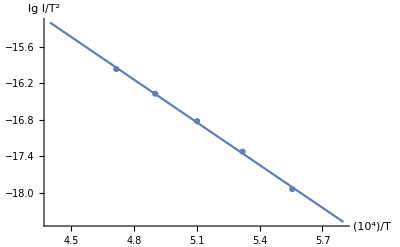

```mathematica
Clear[x1,x2,k,b]
x1=10000/T;
x2=Log[10,10^lgI/T^2]-6;
tab2=Minimize[Total[(k x1+b-x2)^2],{k,b}];
k=(k/.tab2[[2]]);b=(b/.tab2[[2]]);
Show[Plot[k x+b,{x,4.4,5.8},PlotRange->All,AxesLabel->{"10^4/T","lg I/T^2"}],ListPlot[Transpose@{x1,x2},PlotMarkers->Automatic]]
```

```mathematica
k=-2.34610961,b=-4.87728
```

```mathematica
Subscript[e, ϕ]=(10^4 k)/-5040=4.65498eV                 (*work function of W*)
```

```mathematica
Subscript[E, r]=(4.54-4.65498)/4.65498=0.0247
```

```mathematica
密里根油滴实验
```

```mathematica
U(V)    Subscript[t, g](s)    Subscript[t, e](s)
```

```mathematica
Subscript[drop, 1]={{225,220,375,283,575},{18.56,18.94,18.55,18.63,18.75},{27.37,28.84,11.21,17.17,5.59}};
Subscript[drop, 2]={{45,137,62,95,161},{24.22,24.1,24.35,24.27,24.26},{6.18,2.61,6.92,4.05,2.18}};
Subscript[drop, 3]={{244,342,505,613,487},{18.92,18.65,18.70,18.97,18.75},{36.85,16.49,8.80,6.75,9.30}};
Subscript[drop, 4]={{395,374,334,199,417},{8.89,9.11,8.79,8.83,8.85},{5.01,6.73,8.03,33.50,5.38}};
Subscript[drop, 5]={{244,342,515,613,487},{18.92,18.65,18.70,18.97,18.75},{36.85,16.49,8.80,6.75,9.30}};
Subscript[drop, 6]={{367,453,538,651,680},{57.19,62.86,57.20,65.62,65.17},{23.28,17.32,14.80,11.22,9.35}};                                   (*原始数据*)
```

```mathematica
Table[Total[Subscript[drop, i][[2]]]/Length@Subscript[drop, i][[2]],{i,1,6}]   (*下落时间平均*)
```

{18.686,24.24,18.798,8.894,18.798,61.608}

```mathematica
η=1.83*10^-5;P=1.01*10^5;g=9.8;b=0.0082061;d=5*10^-3;l=0.0015;
ρ=981;
Table[Subscript[q, i,j]=N[(18π)/(√(2 ρ g))((η l)/(1+b/(P √((9 η l)/(2ρ Subscript[drop, i][[2]][[j]])))))^(3/2)d/(Subscript[drop, i][[1]][[j]])(1/(Subscript[drop, i][[3]][[j]])+1/(Subscript[drop, i][[2]][[j]]))√(1/(Subscript[drop, i][[3]][[j]]))],{i,1,6},{j,1,5}];
Table[Total@%[[j]]/5,{j,1,6}]                       (*电量*)
```

{9.40517×10^-19,1.49266×10^-17,8.53931×10^-19,2.34274×10^-18,8.50095×10^-19,3.771×10^-19}

```mathematica
Q=Table[Subscript[q, i,j],{i,1,6},{j,1,5}];
c=Table[Total@Q[[j]]/6,{j,1,6}]/(1.6*10^-19)
(*与e精确值对标*)
```

{4.89853,77.7426,4.44756,12.2018,4.42758,1.96406}

```mathematica
Abs[Round[c]-c]/c         (*误差*)
```

{0.0207153,0.00331083,0.10063,0.0165361,0.0965718,0.0182987}

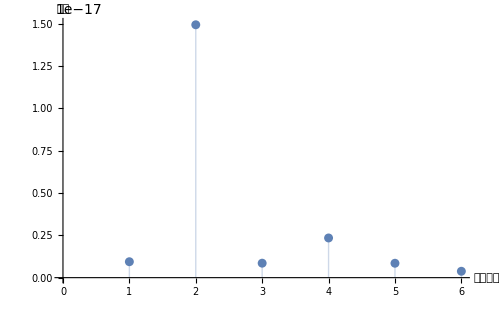

```mathematica
ListPlot[{9.40517*10^-19,1.49266*10^-17,8.53931*10^-19,2.34274*10^-18,8.50095*10^-19,3.771*10^-19},Filling->Axis,ImageSize->500,PlotRange->{0,1.5*10^-17},AxesLabel->{油滴编号,电量}]
```

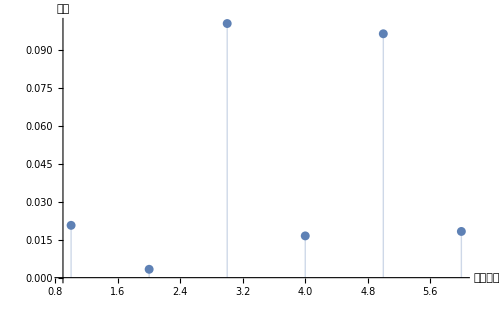

```mathematica
ListPlot[Abs[Round[c]-c]/c,Filling->Axis,ImageSize->500,PlotRange->All,AxesLabel->{油滴编号,误差}]
```

```mathematica
表面张力实验
```

```mathematica
F=Table[0.005i,{i,1,7}];
U1={0.0105,0.0190,0.0279,0.0354,0.0447,0.0529,0.0623};
U2={0.0045,0.0113,0.0254,0.0336,0.0429,0.0513,0.0623};
U3={0.0248,0.0955,0.0965,0.0978,0.0978};
U4={-0.102,0.0593,0.0606,0.0617,0.0615};
D1=0.03496;D2=0.0331;
```

```mathematica
U12=(U1+U2)/2
U34=U3-U4
```

{0.0075,0.01515,0.02665,0.0345,0.0438,0.0521,0.0623}

{0.1268,0.0362,0.0359,0.0361,0.0363}

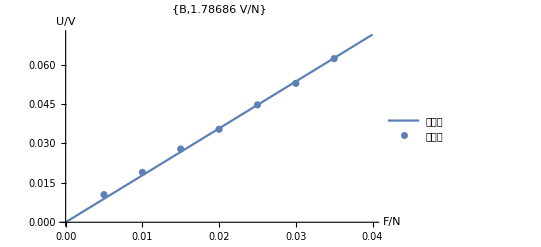

```mathematica
Clear[B]
B=B/.Minimize[Sum[(B F[[i]]-U1[[i]])^2,{i,1,7}],B][[2]];
Show[Plot[B f,{f,0,0.04},AxesLabel->{"F/N","U/V"},PlotLabel->{"B",B"V/N"},PlotLegends->{"拟合值"},ImageSize->400],ListPlot[Transpose@{F,U1},PlotLegends->{"实验值"}]]
```

```mathematica
α=(Subscript[U, 1]-Subscript[U, 2])/(B π(Subscript[D, 1]+Subscript[D, 2]))
```

```mathematica
α=1/4 Sum[(U3[[i]]-U4[[i]])/(B π(D1+D2)),{i,2,5}]
(α-0.07275)/α//N
```

```mathematica
B=1.78686V/m
α=0.094553N/m
```

```mathematica
ϵ=0.23059
```

```mathematica
干涉法测热膨胀实验
```

```mathematica
λ=632.8*10^-6;Subscript[l, 0]=150;Subscript[t, 0]=25;Subscript[α, standard]=2.08*10^-5;
Subscript[T, record]=Table[5t+30,{t,0,6}];
T=Table[5t+32.5,{t,0,5}];
n={47,49,46,47,43,40};
```

```mathematica
Δl=(n λ)/2
α=Table[Δl[[i]]/(Subscript[l, 0](Subscript[T, record][[i+1]]-Subscript[T, record][[i]])),{i,1,6}]
```

{0.0148708,0.0155036,0.0145544,0.0148708,0.0136052,0.012656}

{0.0000198277,0.0000206715,0.0000194059,0.0000198277,0.0000181403,0.0000168747}

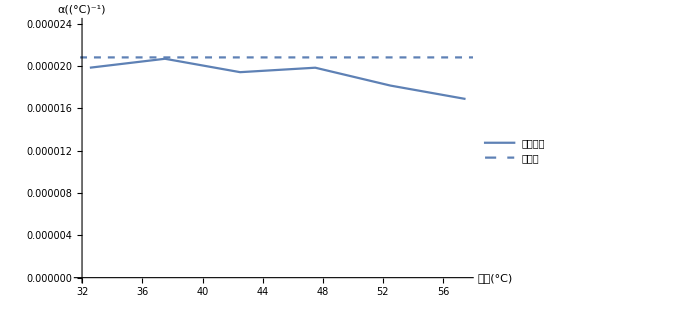

```mathematica
Show[ListLinePlot[Transpose@{T,α},ImageSize->500,PlotRange->{0,0.000024},AxesLabel->{"温度(°C)","α((°C)^-1)"},PlotLegends->{"本次实验"}],Plot[2.08*10^-5,{t,30,60},PlotStyle->Dashed,PlotLegends->{"标准值"}]]
```

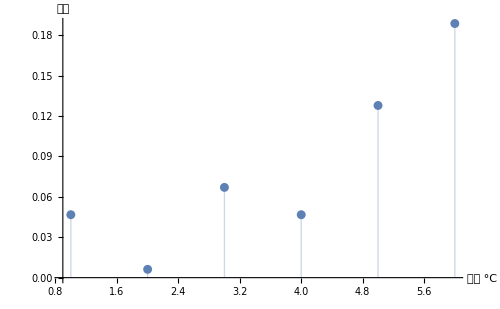

```mathematica
ListPlot[Abs[α-Subscript[α, standard]]/Subscript[α, standard],Filling->Axis,ImageSize->500,PlotRange->All,AxesLabel->{温度(°C),误差}]
```

```mathematica
Total[Abs[α-Subscript[α, standard]]/Subscript[α, standard]]/Length@α                                 (*平均误差*)
```

0.080547

```mathematica
T∝Subscript[E, k]∝v^2,α∝(∂r̄)/(∂T)∝(∂Subscript[E, p])/(∂T),Subscript[E, k]∝Subscript[E, p]->α∝(∂Subscript[E, p])/(∂T)∝(∂T)/(∂T)=1
```

```mathematica
(∂^2 Subscript[E, p])/(∂(r̄)^2)>0   (∂α)/(∂T)∝(∂^2 r̄)/(∂T^2)∝(∂^2 Subscript[E, p])/(∂T^2)
```

```mathematica
霍尔效应及其应用
```

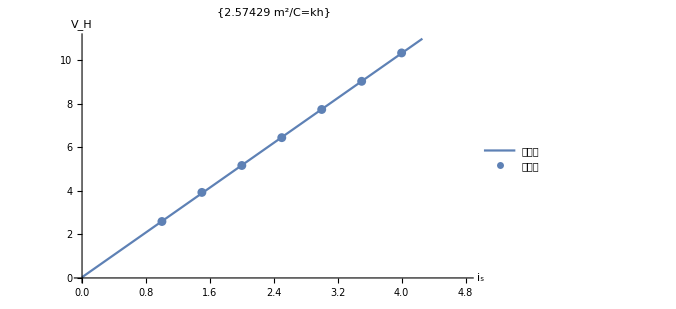

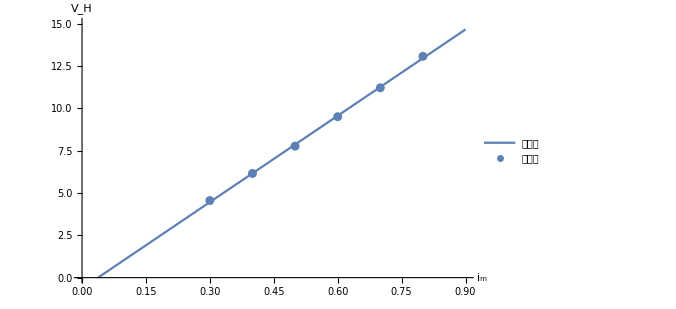

```mathematica
Subscript[i, s]=Table[1+0.5i,{i,0,6}];Subscript[i, m]=Table[0.3+0.1i,{i,0,5}];Subscript[x, 1]={2,3,4,7,10,13,16,19,20,21};
Evaluate@Table[Subscript[Vs, i],{i,1,4}]={{-2.66,-3.98,-5.30,-6.61,-7.94,-9.27,-10.61},{2.53,4,5.32,6.63,7.96,9.29,10.63},{-2.52,-3.76,-5.02,-6.27,-7.53,-8.79,-10.06},{2.67,3.99,5.04,6.29,7.55,8.81,10.08}};
Evaluate@Table[Subscript[Vm, i],{i,1,4}]={{-4.74,-6.4,-7.95,-9.69,-11.4,-13.8},{4.76,6.42,7.98,9.71,11.42,13.1},{-4.35,-5.89,-7.55,-9.29,-10.99,-12.67},{4.36,5.9,7.57,9.31,11.01,12.69}};
Evaluate@Table[Subscript[Vx, i],{i,1,4}]={{-0.72,-0.36,-0.1,0.19,0.2,0.21,0.16,-0.11,-0.4,-0.82},{-2.06,-2.42,-2.68,-2.97,-2.99,-2.99,-2.94,-2.67,-2.38,-1.95},{-0.47,-0.02,0.25,0.46,0.52,0.52,0.47,0.18,-0.11,-0.52},{-2.31,-2.76,-3.03,-3.25,-3.31,-3.3,-3.25,-2.97,-2.67,-2.25}};
Subscript[V, Hs]=Total@Table[Abs@Subscript[Vs, i],{i,1,4}]/4;
Subscript[V, Hm]=Total@Table[Abs@Subscript[Vm, i],{i,1,4}]/4;
Subscript[V, Hx]=Total@Table[Abs@Subscript[Vx, i],{i,1,4}]/4;
tab1=Minimize[Evaluate@Total@Table[(kh Subscript[i, s][[n]]+b-Subscript[V, Hs][[n]])^2,{n,1,Length@Subscript[i, s]}],{kh,b}];
tab2=Minimize[Evaluate@Total@Table[(k Subscript[i, m][[n]]+Subscript[b, 2]-Subscript[V, Hm][[n]])^2,{n,1,Length@Subscript[i, m]}],{k,Subscript[b, 2]}];
kh=kh/.(tab1[[2]]);
b=b/.(tab1[[2]]);
k=k/.(tab2[[2]]);
Subscript[b, 2]=Subscript[b, 2]/.(tab2[[2]]);
Show[Plot[kh i+b,{i,0,4.8},ImageSize->500,PlotRange->{0,11},PlotLabel->{kh"m^2/C=kh"},PlotLegends->{拟合值},AxesLabel->{"i_s","V_H"}],ListPlot[Transpose@{Subscript[i, s],Subscript[V, Hs]},ImageSize->500,PlotRange->All,AxesLabel->{工作电流,电压},PlotLegends->{实验值}]]
Show[Plot[k i+Subscript[b, 2],{i,0,.9},ImageSize->500,PlotRange->{0,15},PlotLegends->{拟合值},AxesLabel->{"i_m","V_H"}],ListPlot[Transpose@{Subscript[i, m],Subscript[V, Hm]},ImageSize->500,PlotRange->All,AxesLabel->{工作电流,电压},PlotLegends->{实验值}]]
```

```mathematica
Subscript[R, H]=kh d=0.0012871428571428589(m^3/C)
```

```mathematica
B=8 π^2 μ∫_(-l/2)^(l/2) (i R)/((R^2+(x-Subscript[x, 0])^2)^(3/2))ⅆ Subscript[x, 0]=(i μ π^2)/R ((l-2 x)/(√(4 R^2+(l-2 x)^2))+(l+2 x)/(√(4 R^2+(l+2 x)^2))) =A((l-x)/(√(B+(l-x)^2))+(l+x)/(√(B+(l+x)^2)))
```

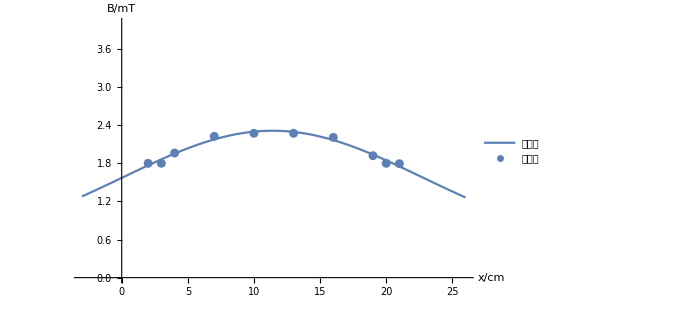

```mathematica
im=0.3;
B=Subscript[V, Hx]/(kh im);
tab3=Minimize[Evaluate@Total@Table[(A((l-Subscript[x, 1][[n]]+x0)/(√(F+(l-Subscript[x, 1][[n]]+x0)^2))+(l+Subscript[x, 1][[n]]-x0)/(√(F+(l+Subscript[x, 1][[n]]-x0)^2)))-B[[n]])^2,{n,1,Length@Subscript[x, 1]}],{A,F,l,x0}];
A=A/.(tab3[[2]]);
F=F/.(tab3[[2]]);
l=l/.(tab3[[2]]);
x0=x0/.(tab3[[2]]);
Show[Plot[A((l-x+x0)/(√(F+(l-x+x0)^2))+(l+x-x0)/(√(F+(l+x-x0)^2))),{x,-3,26},ImageSize->500,PlotRange->{0,4},PlotLegends->{拟合值},AxesLabel->{"x/cm","B/mT"}],ListPlot[Transpose@{Subscript[x, 1],B},ImageSize->500,PlotRange->All,AxesLabel->{工作电流,电压},PlotLegends->{实验值}]]
```

```mathematica
Grid[{Flatten@{"i_s/mA",Subscript[i, s]},Flatten@{"V_Hs",Subscript[V, Hs]}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.08],All}},Background->{None,{GrayLevel[0.7],{White}}}]
Grid[{Flatten@{"i_m/A",Subscript[i, m]},Flatten@{"V_Hs",Subscript[V, Hm]}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.08],All}},Background->{None,{GrayLevel[0.7],{White}}}]
Grid[{Flatten@{"x/cm",Subscript[x, 1]},Flatten@{"B",B}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.08],All}},Background->{None,{GrayLevel[0.7],{White}}}]
```

i_s/mA | 1. | 1.5 | 2. | 2.5 | 3. | 3.5 | 4.
V_Hs | 2.595 | 3.9325 | 5.17 | 6.45 | 7.745 | 9.04 | 10.345

i_m/A | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8
V_Hs | 4.5525 | 6.1525 | 7.7625 | 9.5 | 11.205 | 13.065

x/cm | 2 | 3 | 4 | 7 | 10 | 13 | 16 | 19 | 20 | 21
B | 1.79985 | 1.79985 | 1.96171 | 2.22392 | 2.27248 | 2.27248 | 2.20773 | 1.91963 | 1.79985 | 1.79338

```mathematica
弗兰克-赫兹实验
```

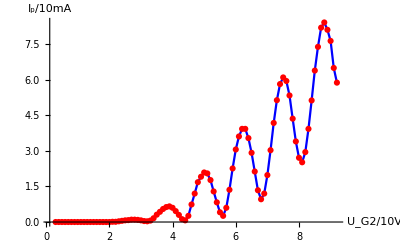

```mathematica
Clear[Subscript]
Subscript[U, G2]=Table[0.3+0.1u,{u,0,89}];
Subscript[i, p]=Flatten@{Table[0,{i,1,18}],{0.01,0.01,0.03,0.05,0.07,0.08,0.1,0.1,0.09,0.07,0.04,0.03,0.06,0.16,0.31,0.43,0.55,0.63,0.66,0.6,0.46,0.3,0.12,0.07,0.26,0.74,1.2,1.68,1.91,2.09,2.05,1.77,1.29,0.83,0.41,0.26,0.6,1.36,2.26,3.06,3.61,3.93,3.93,3.54,2.92,2.13,1.34,0.96,1.2,1.98,3.03,4.18,5.14,5.82,6.1,5.95,5.34,4.36,3.4,2.71,2.52,2.95,3.93,5.13,6.39,7.39,8.2,8.42,8.11,7.64,6.5,5.88}};
Show[ListLinePlot[Transpose@{Subscript[U, G2],Subscript[i, p]},PlotStyle->Blue,PlotRange->All,ImageSize->400,AxesLabel->{"U_G2/10V","I_p/10mA"}],ListPlot[Transpose@{Subscript[U, G2],Subscript[i, p]},PlotStyle->Red,PlotRange->All,ImageSize->400]]
```

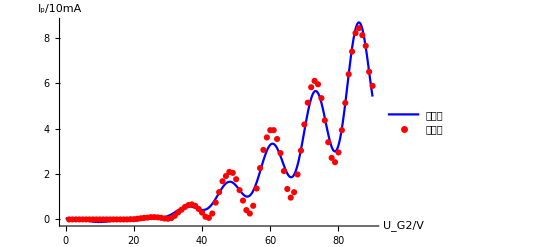

U_0=

12.7815

```mathematica
Clear[Subscript,m,sol1,a,ω,φ]
Subscript[U, G2]=Table[0.3+0.1u,{u,0,89}];
Subscript[i, p]=Flatten@{Table[0,{i,1,18}],{0.01,0.01,0.03,0.05,0.07,0.08,0.1,0.1,0.09,0.07,0.04,0.03,0.06,0.16,0.31,0.43,0.55,0.63,0.66,0.6,0.46,0.3,0.12,0.07,0.26,0.74,1.2,1.68,1.91,2.09,2.05,1.77,1.29,0.83,0.41,0.26,0.6,1.36,2.26,3.06,3.61,3.93,3.93,3.54,2.92,2.13,1.34,0.96,1.2,1.98,3.03,4.18,5.14,5.82,6.1,5.95,5.34,4.36,3.4,2.71,2.52,2.95,3.93,5.13,6.39,7.39,8.2,8.42,8.11,7.64,6.5,5.88}};
m=3;a=2.5;
sol1=NMinimize[{Sum[((Sin[ω U+φ]+a)∑_(ι=0)^m Subscript[A, ι] U^ι-Subscript[i, p][[U]])^4,{U,1,Length@Subscript[U, G2]}]},Flatten@{Table[Subscript[A, ι],{ι,0,m}],ω,φ},MaxIterations->999];
Evaluate@Flatten@{Table[Subscript[A, ι],{ι,0,m}],ω,φ}=Evaluate@Flatten@{Table[Subscript[A, ι],{ι,0,m}],ω,φ}/.sol1[[2]];
Show[Plot[(Sin[ω U+φ]+a)∑_(ι=0)^m Subscript[A, ι] U^ι,{U,0,Length@Subscript[i, p]},PlotStyle->Blue,PlotRange->All,ImageSize->400,AxesLabel->{"U_G2/V","I_p/10mA"},PlotLegends->{"拟合值"}],ListPlot[Subscript[i, p],PlotStyle->Red,PlotRange->All,ImageSize->400,PlotLegends->{"实验值"}]]
"U_0="
Abs[2π/ω]
```

```mathematica
(12.7815197499-11.3)/11.3
```

0.131108

```mathematica
λ=(ℏ c)/Subscript[U, 0]=9.6972*10^-8(m)
Subscript[U, 0 accu]=11.3(V)
Subscript[ϵ, U]=(|Subscript[U, 0]-Subscript[U, 0 accu]|)/Subscript[U, 0 accu]=0.13110794
Subscript[λ, accu]=1.22*10^-7(m)
Subscript[ϵ, λ]=(|λ-Subscript[λ, accu]|)/Subscript[λ, accu]=0.20514754
```

```mathematica
光栅光谱仪
```

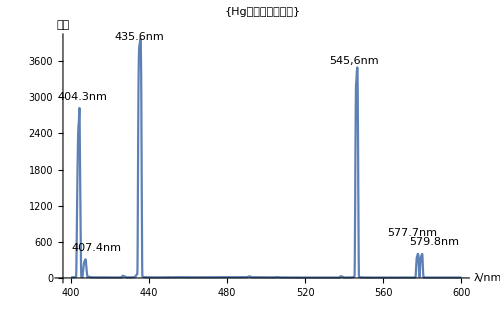

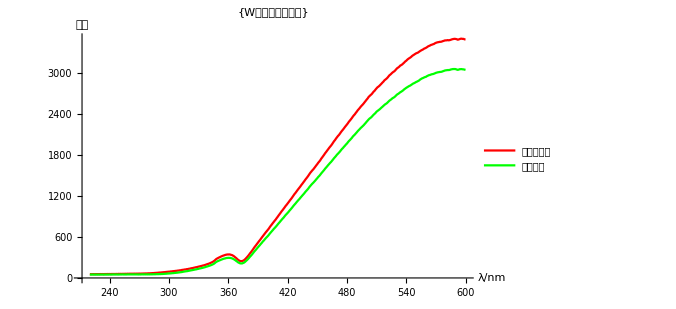

```mathematica
tabHg=Flatten[Import@"C:\\Users\\Teacher Computerium\\Documents\\大学物理实验2\\光栅光谱仪实验数据\\Hg.xlsx",1];
tabW=Flatten[Import@"C:\\Users\\Teacher Computerium\\Documents\\大学物理实验2\\光栅光谱仪实验数据\\W.xlsx",1];
tabWG=Flatten[Import@"C:\\Users\\Teacher Computerium\\Documents\\大学物理实验2\\光栅光谱仪实验数据\\W_with_Glass.xlsx",1];
ListLinePlot[tabHg,PlotRange->All,ImageSize->500,AxesLabel->{"λ/nm",光强},PlotLabel->{Hg气体的发射光谱},Epilog->{Text["404.3nm",{406,3000}],Text["407.4nm",{413,500}],Text["435.6nm",{435,4000}],Text["545,6nm",{545,3600}],Text["577.7nm",{575,750}],Text["579.8nm",{586,600}]}]
ListLinePlot[{tabW,tabWG},PlotRange->All,ImageSize->500,PlotStyle->{Red,Green},AxesLabel->{"λ/nm",光强},PlotLegends->{未加玻璃片,加玻璃片},PlotLabel->{W固体的发射光谱}]
```

```mathematica
双光栅测微振动
```

f/Hz | 510. | 510.1 | 510.2 | 510.3 | 510.4 | 510.5 | 510.6 | 510.7 | 510.8 | 510.9
N | 0.6 | 0.7 | 0.9 | 1.1 | 1.4 | 1.5 | 1.8 | 2.6 | 3.5 | 4.8

f/Hz | 511. | 511.1 | 511.2 | 511.3 | 511.4 | 511.5 | 511.6 | 511.7 | 511.8 | 511.9 | 512.
N | 7.5 | 10.6 | 5.2 | 3.8 | 2.2 | 1.6 | 1.5 | 1.3 | 1.1 | 0.8 | 0.7

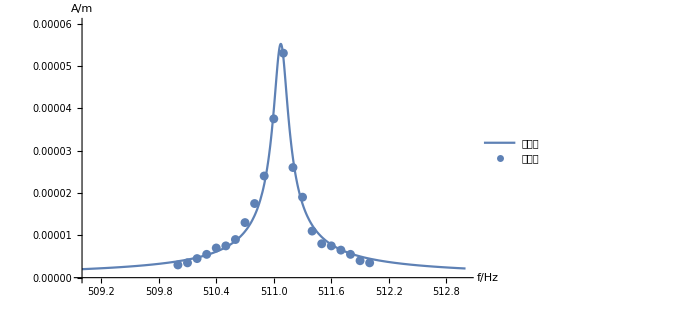

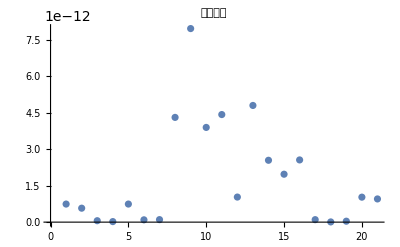

```mathematica
Clear[a,b,F,sol]
tabf=Table[510+.1f,{f,0,20}];
tabN={.6,.7,.9,1.1,1.4,1.5,1.8,2.6,3.5,4.8,7.5,10.6,5.2,3.8,2.2,1.6,1.5,1.3,1.1,0.8,0.7};
d=10^-5;
tabA=d/2 tabN;
sol=NMinimize[{Sum[(a/(√(b+(F/tabf[[f]]-tabf[[f]]/F)^2))-tabA[[f]])^2,{f,1,Length@tabf}],a>0,.00001>b>0,512>F>510},{a,b,F},MaxIterations->999,Method->"SimulatedAnnealing"];
{a,b,F}={a,b,F}/.sol[[2]];
Grid[{Flatten@{"f/Hz",Take[tabf,{1,10}]},Flatten@{"N",Take[tabN,{1,10}]}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.08],All}},Background->{None,{GrayLevel[0.7],{White}}}]
Grid[{Flatten@{"f/Hz",Take[tabf,{11,21}]},Flatten@{"N",Take[tabN,{11,21}]}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.08],All}},Background->{None,{GrayLevel[0.7],{White}}}]
Show[Plot[a/(√(b+(F/f-f/F)^2)),{f,509,513},ImageSize->500,PlotRange->{0,6*10^-5},PlotLegends->{拟合值},AxesLabel->{"f/Hz","A/m"}],ListPlot[Transpose@{tabf,tabA},ImageSize->500,PlotRange->{0,6*10^-5},AxesLabel->{频率,振幅},PlotLegends->{实验值}]]
ListPlot[Table[(a/(√(b+(F/tabf[[f]]-tabf[[f]]/F)^2))-tabA[[f]])^2,{f,1,Length@tabf}],PlotLabel->"拟合误差"]
```

```mathematica
Clear["`*",Subscript,b,a,q,B,im]
```

```mathematica
Quit[]
```